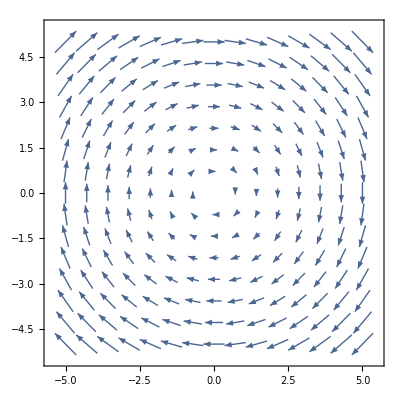

```mathematica
a1=0;
a2=0;
A=1;
B=1;
VectorPlot[{y,0},{x,-5,5},{y,-5,5}];
VectorPlot[{0,-x},{x,-5,5},{y,-5,5}];
VectorPlot[{A(y+a1 x),B(-x+ a2 y)},{x,-5,5},{y,-5,5}]
```

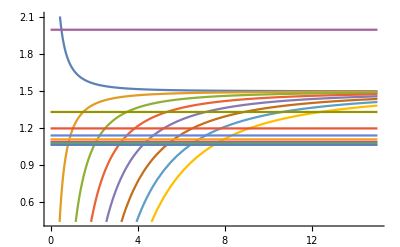

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Plot[{gL[j,0],gL[j,1],gL[j,2],gL[j,3],gL[j,4],gL[j,5],gL[j,6],gL[j,7],gL[1/2,0],gL[3/2,1],gL[5/2,2],gL[7/2,3],gL[9/2,4],gL[11/2,5],gL[13/2,6],gL[15/2,7]},{j,0,15}]
```

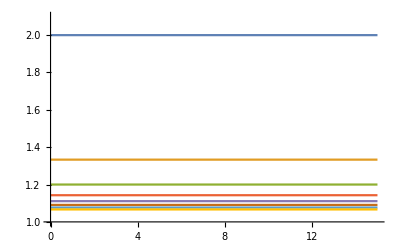

2

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Plot[{gL[1/2,0],gL[3/2,1],gL[5/2,2],gL[7/2,3],gL[9/2,4],gL[11/2,5],gL[13/2,6],gL[15/2,7]},{j,0,15},PlotRange->{1,2.1}]
```

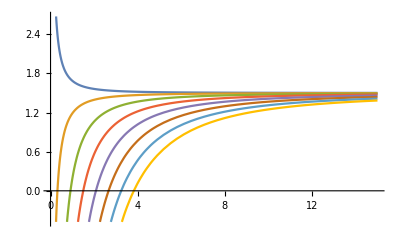

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Plot[{gL[j,0],gL[j,1],gL[j,2],gL[j,3],gL[j,4],gL[j,5],gL[j,6],gL[j,7]},{j,0,15}]
```

```mathematica
gL[j_,l_,s_]:=1+(j(j+1)-l(l+1)+s(s+1))/(2j(j+1))
FullSimplify[gL[l+1/2,l,1/2]]
```

1+1/(1+2 l)

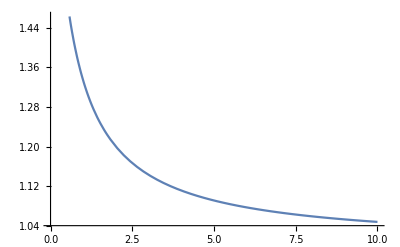

```mathematica
Plot[1+1/(1+2 l),{l,0,10}]
```

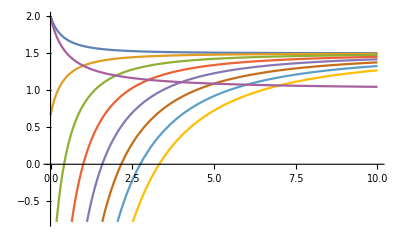

```mathematica
Plot[{gL[l+1/2,0],gL[l+1/2,1],gL[l+1/2,2],gL[l+1/2,3],gL[l+1/2,4],gL[l+1/2,5],gL[l+1/2,6],gL[l+1/2,7],1+1/(1+2 l)},{l,0,10}]
```

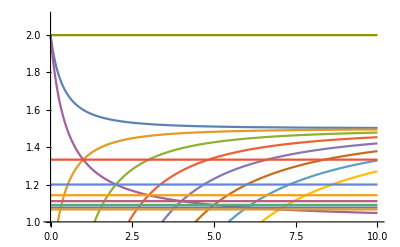

```mathematica
Plot[{gL[l+1/2,0],gL[l+1/2,1],gL[l+1/2,2],gL[l+1/2,3],gL[l+1/2,4],gL[l+1/2,5],gL[l+1/2,6],gL[l+1/2,7],1+1/(1+2 l),gL[1/2,0],gL[3/2,1],gL[5/2,2],gL[7/2,3],gL[9/2,4],gL[11/2,5],gL[13/2,6],gL[15/2,7]},{l,0,10},PlotRange->{1,2.1}]
```

```mathematica
Plot3D[gL[j,l],{j,-5,5},{l,-5,5}]
```

-Graphics3D-